```mathematica
ASSIGNMENT - 1
```

Om Gupta
214047

```mathematica
eqn1=D[y[x],x]==Sin[x];
DSolve[eqn1,y[x],x]
```

```mathematica
{{y[x]->C[1]-Cos[x]}}
```

```mathematica
eqn2=D[y[x],x]-y[x]==Sin[x];
DSolve[eqn2,y[x],x]
```

```mathematica
{{y[x]->ⅇ^x C[1]+1/2 (-Cos[x]-Sin[x])}}
```

```mathematica
eqn3 = D[y[x], x] == (x - y[x]) / (x + y[x]);
DSolve[eqn3, y[x], x]
```

```mathematica
{{y[x]->-x-√(ⅇ^(2 C[1])+2 x^2)},{y[x]->-x+√(ⅇ^(2 C[1])+2 x^2)}}
```

```mathematica
eqn4 = D[y[x], x] == (x + y[x]) / (x - y[x]);
DSolve[eqn4, y[x], x]
```

Solve[-ArcTan[y[x]/x]+1/2 Log[1+y[x]^2/x^2]==C[1]-Log[x],y[x]]

```mathematica
sol1 = DSolve[{D[y[x], x] == y[x] / x, y[1] == 2}, y[x], x]
```

{{y[x]→2 x}}

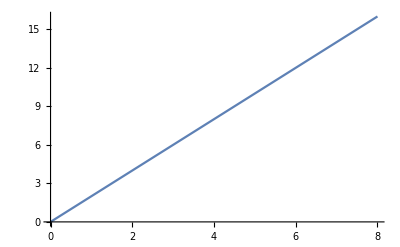

```mathematica
Plot[y[x] = 2 x, {x, 0, 8}]
```

```mathematica
DSolve[{y'[x] == y[x]}, y[x], x]
```

{{y[x]→ⅇ^x C[1]}}